## Background

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

## Distances

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]];
```

```mathematica
exportDistance[a_,b_]:=
Module[{distance,name},
distance=distances[a,b];
name=StringJoin[ToString[a],"and",ToString[b],".mx"];
Export[FileNameJoin[{dataDirectory,name}],distance]]
```

```mathematica
Do[exportDistance[a,b],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates]}]
```

```mathematica
test=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData/1and2.mx"];
```

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
```

```mathematica
Module[{currentPairData,data},
data=Table[
currentPairData=DeleteCases[Import[FileNameJoin[{dataDirectory,name}]],Indeterminate];
{Median[currentPairData],Mean[currentPairData]},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
```

```mathematica
Export[FileNameJoin[{dataDirectory,"medians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"means.mx"}],means];
```

```mathematica
medians = Import[FileNameJoin[{dataDirectory,"medians.mx"}]];
means = FileNameJoin[{dataDirectory,"means.mx"}];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Missing[]}].

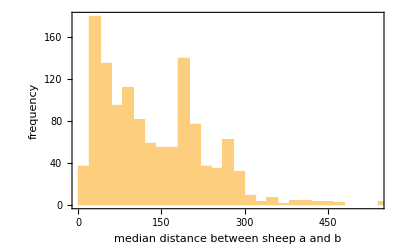

```mathematica
Histogram[medians,Frame->True,FrameLabel->{"median distance between sheep a and b","frequency"}]
```

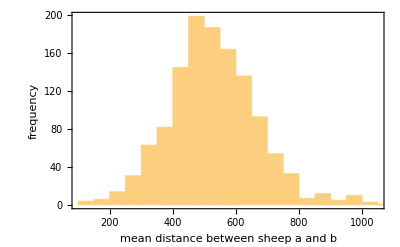

```mathematica
Histogram[means,Frame->True,FrameLabel->{"mean distance between sheep a and b","frequency"}]
```

```mathematica
Dynamic[{a,b}]
```

## Distribution

```mathematica
randomDistances=Select[Table[EuclideanDistance@@rawCoordinates2[[RandomInteger[{1,Length[rawCoordinates2]},2],RandomInteger[{1,Length[rawCoordinates2[[1]]]}]]],200000],#>0&]
```

{12.7675,15.3687,145.067,1290.,2272.46,182887,11.793,14.7627,6.54457,2390.62,901.03}
 |  |  |  |

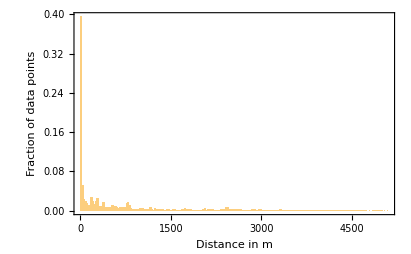

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

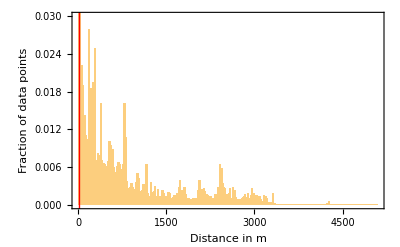

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
Histogram[randomDistances,{50},Frame->True,FrameLabel->{"Distance","count"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

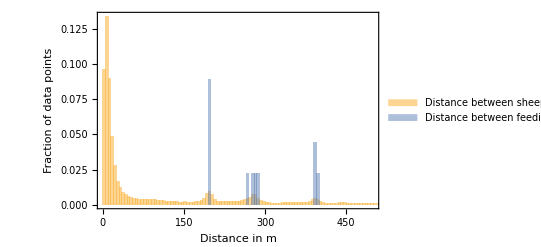

```mathematica
Histogram[{randomDistances,feedingStationsDistances},{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"},ChartLegends->{"Distance between sheep","Distance between feeding stations"}]
```

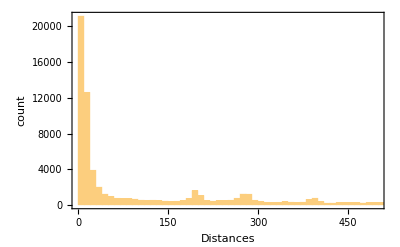

```mathematica
Histogram[randomDistances,{10},PlotRange->{{0,500},All},Frame->True,FrameLabel-> {"Distances","count"}]
```

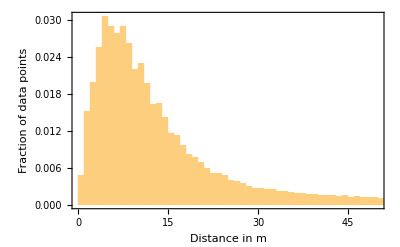

```mathematica
Histogram[randomDistances,{1},"Probability",PlotRange->{{0,50},All},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"}]
```

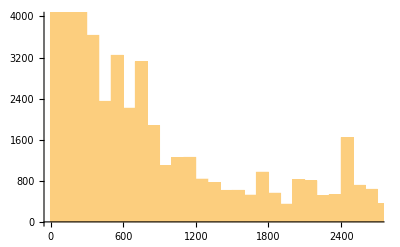

```mathematica
Histogram[randomDistances,PlotRange->{{0,2700},{0,4000}}]
```

```mathematica
RandomSample[#,2]/@RandomSample[Transpose[rawCoordinates2],5]
```

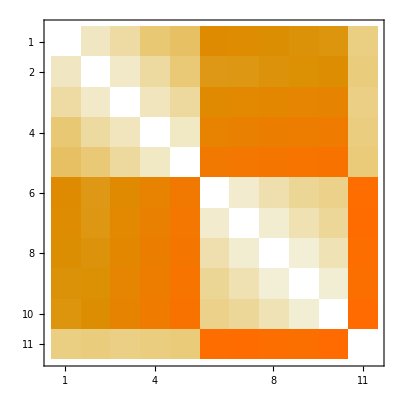

```mathematica
MatrixPlot[DistanceMatrix[N/@Join[feeding,{water}]]]
```

```mathematica
feeding
```

{{581448,6563715},{581450,6563434},{581358,6563183},{581175,6562960},{580935,6562820},{583822,6563068},{583848,6563266},{583860,6563462},{583860,6563657},{583851,6563852}}

```mathematica
EuclideanDistance[water,feeding[[5]]]//N
```

801.302

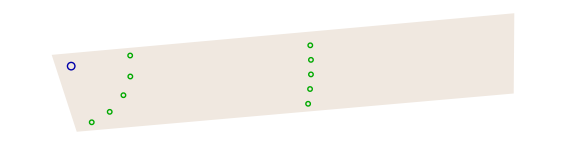

```mathematica
metadataGraphic
```

```mathematica
gif=Animate[Show[metadataGraphic,Graphics[Circle[#,15]&/@DeleteMissing[rawCoordinates[[All,n]],1,2],PlotRange->RegionBounds[paddockRegion]]],{n,1000,15000,10}];
```

```mathematica
Export["SampleMotion.gif",gif]
```

SampleMotion.gif